```mathematica
(*Mathematica*)
```

```mathematica
Clear[ϕ,f,m,r,w,v,sc,g]
```

```mathematica
p[z_]=z^5-z^4-z^3+z^2-1
```

-1+z^2-z^3-z^4+z^5

```mathematica
ϕ=N[GoldenRatio]
```

1.61803

```mathematica
Exp[2*π*I*ϕ]
```

-0.737369-0.67549 ⅈ

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m=Transpose[CompanionMatrix[p[x],x]]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{1,0,-1,1,1}}

```mathematica
N[Eigenvalues[m]]
```

{1.44327,0.609585+0.707177 ⅈ,0.609585-0.707177 ⅈ,-0.831219+0.322384 ⅈ,-0.831219-0.322384 ⅈ}

```mathematica
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
```

```mathematica
v=Table[r[i],{i,5}]
```

{-0.831219-0.322384 ⅈ,-0.831219+0.322384 ⅈ,0.609585-0.707177 ⅈ,0.609585+0.707177 ⅈ,1.44327}

```mathematica
Abs[%]
```

{0.891548,0.891548,0.933645,0.933645,1.44327}

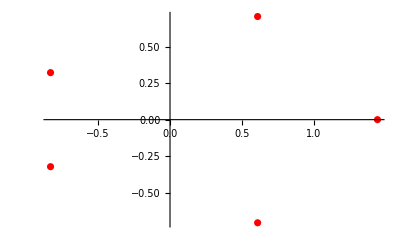

```mathematica
ComplexListPlot[v,PlotStyle->Red]
```

```mathematica
sc=2.0;
```

```mathematica
w={{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[1]],Im[r[1]]},{Re[r[3]],Im[r[3]]}},{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[2]],Im[r[2]]},{Re[r[3]],Im[r[3]]}},{{Re[r[2]],Im[r[2]]},{Re[r[4]],Im[r[4]]}},{{Re[r[3]],Im[r[3]]},{Re[r[4]],Im[r[4]]}}}
```

{{{-0.831219,-0.322384},{-0.831219,0.322384}},{{-0.831219,-0.322384},{0.609585,-0.707177}},{{-0.831219,-0.322384},{-0.831219,0.322384}},{{-0.831219,0.322384},{0.609585,-0.707177}},{{-0.831219,0.322384},{0.609585,0.707177}},{{0.609585,-0.707177},{0.609585,0.707177}}}

```mathematica
Table[Eigenvalues[w[[i]]]//Chop,{i,6}]
```

{{-1.02945,0.520613},{-0.769198+0.438946 ⅈ,-0.769198-0.438946 ⅈ},{-1.02945,0.520613},{-1.21682,-0.321574},{-0.94982,0.825778},{0.658381+0.654755 ⅈ,0.658381-0.654755 ⅈ}}

```mathematica
(* Projecting the  3rd Minimal Pisot Polynomial onto a qz^(2*n) Hermann rings Julia*)
```

```mathematica
f[z_,1]=Exp[2*π*I*ϕ]*z^6*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,2]=Exp[2*π*I*ϕ]*z^8*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,3]=Exp[2*π*I*ϕ]*z^10*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,4]=Exp[2*π*I*ϕ]*z^12*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,5]=Exp[2*π*I*ϕ]*z^14*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
f[z_,6]=Exp[2*π*I*ϕ]*z^16*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
```

```mathematica
g=Table[JuliaSetPlot[f[z,i],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All],{i,6}];
```

General::munfl: (-1.31714×10^-220-1.18318×10^-220 ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.31714×10^-220-1.18318×10^-220 ⅈ)^8 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.31714×10^-220-1.18318×10^-220 ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Export["Julia_5root_3rd_minimal_Pisot_Polynomial_z2n_Herman_rings_Hue_scale2.jpg",GraphicsGrid[{{g[[1]],g[[2]],g[[3]]},{g[[4]],g[[5]],g[[6]]}},ImageSize->{6000,4000}]]
```

Julia_5root_3rd_minimal_Pisot_Polynomial_z2n_Herman_rings_Hue_scale2.jpg

```mathematica
(*end*)
```